```mathematica
n := 3
k := (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

```mathematica
k
```

5.71202×10^-36

```mathematica
cte := k/2*ati^4/(Sinh[√(2k)*ti])^2
```

```mathematica
cte
```

1.78335×10^-35

```mathematica
a3[t_]:= ((2*cte)/k)^(1/4)*√Sinh[√(2 k)t]
```

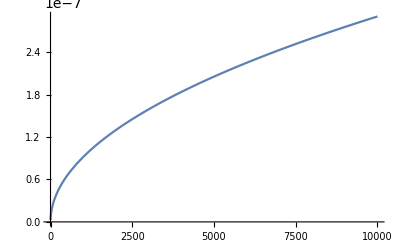

```mathematica
Plot[a3[t], {t, ti, 10000}]
```

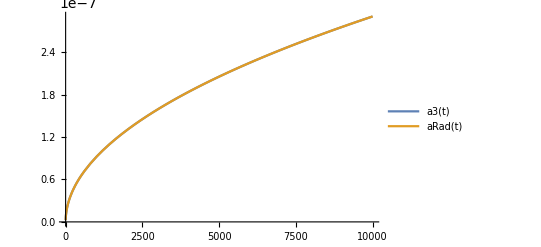

```mathematica
Plot[{a3[t], aRad[t]}, {t, ti, 10000}, PlotLegends->"Expressions"]
```

```mathematica
a3exp[t_]:= Exp[√(2/k)t]
```

```mathematica
Plot[a3exp[t], {t, ti, 10000}]
```

-Graphics-

```mathematica
√(2/k)
```

5.91725×10^17